```mathematica
Solve[1.4==8.314Log[P/2280],P]
```

{{P→2698.15}}

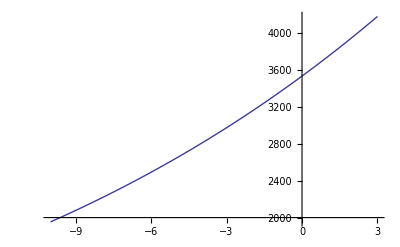

```mathematica
Plot[1000* E^(-8.433613 Log[T+273.15]-6281.040/(T+273.15)+71.10718+6.198413*10^(-6)*(T+273.15)^2),{T,-10,3}]
```

```mathematica
1000/268.15
```

3.72926

```mathematica
List1={{30,4.8},{60,5.13},{90,5.377},{120,5.641},{150,5.921},{180,6.184},{210,6.448},{240,6.661},{270,6.924},{300,7.187},{330,7.417},{360,7.664},{390,7.894},{420,8.14}};
```

```mathematica
f=Interpolation[List1]
```

InterpolatingFunction[{{30.,420.}},<>]

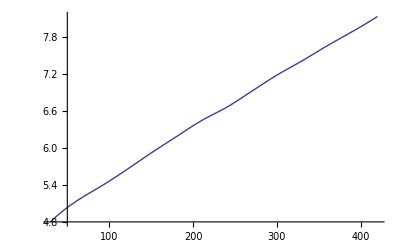

```mathematica
Plot[%112[x],{x,30.,420.}]
```

```mathematica
List3={};
For[i=1,i≤12,i++,
AppendTo[List3,D[f[x],x]/.x->(30+30*i)]]
```

```mathematica
List3
```

{0.00906111,0.00796111,0.00907222,0.00923333,0.00868333,0.00823889,0.00737222,0.00904444,0.0084,0.00767222,0.00813889,0.00775}

```mathematica
Directory[]
```

D:\用户目录\Documents

```mathematica
SetDirectory["D:\物理实验A（1）"]
```

SetDirectory::cdir: 不能把当前目录设为 "D:\\:7269\:7406\:5b9e\:9a8cA\:ff081\:ff09".

$Failed

```mathematica
SetDirectory["/物理实验A（1）"]
```

D:\物理实验A（1）

```mathematica
Directory[]
```

D:\物理实验A（1）

```mathematica
Expand[(x+y)^2]>>tmp
```

```mathematica
List2<<tmp
```

7.89365 List2

```mathematica
List2
```

List2

```mathematica
<<tmp
```

7.89365

```mathematica
List21=ReadList["tmp",Number]
```

{7.20376,7.48309,7.7623,8.02498,8.30397,8.58284,8.8616,9.12385,9.36962,9.63168,9.8609,10.1228,10.3845,10.6462}

```mathematica
List22=Table[{i*30,List21[[i]]},{i,1,14}]
```

{{30,7.20376},{60,7.48309},{90,7.7623},{120,8.02498},{150,8.30397},{180,8.58284},{210,8.8616},{240,9.12385},{270,9.36962},{300,9.63168},{330,9.8609},{360,10.1228},{390,10.3845},{420,10.6462}}

```mathematica
Length[%]
```

14

```mathematica
#^(5/4)&/@List2
```

{7.72025,8.18811,8.69292,9.23557,9.75198,10.2737,10.7014,11.2324,11.7682,12.2409,12.7513,13.2311}

```mathematica
List2=%
```

{7.72025,8.18811,8.69292,9.23557,9.75198,10.2737,10.7014,11.2324,11.7682,12.2409,12.7513,13.2311}

```mathematica
{List2,List3}//Transpose
```

{{7.72025,0.00906111},{8.18811,0.00796111},{8.69292,0.00907222},{9.23557,0.00923333},{9.75198,0.00868333},{10.2737,0.00823889},{10.7014,0.00737222},{11.2324,0.00904444},{11.7682,0.0084},{12.2409,0.00767222},{12.7513,0.00813889},{13.2311,0.00775}}

```mathematica
Transpose[%]
```

{{0.00906111,7.72025},{0.00796111,8.18811},{0.00907222,8.69292},{0.00923333,9.23557},{0.00868333,9.75198},{0.00823889,10.2737},{0.00737222,10.7014},{0.00904444,11.2324},{0.0084,11.7682},{0.00767222,12.2409},{0.00813889,12.7513},{0.00775,13.2311}}

```mathematica
LinearModelFit[%,x,x]
```

FittedModel[0.0103024-«23» x]

```mathematica
6.847/0.0103024//N
```

664.602

```mathematica
(668.80-%)/%//N
```

0.00631592

```mathematica
f2=Interpolation[List22]
```

InterpolatingFunction[{{30.,420.}},<>]

```mathematica
List31=ReadList["tmp",Number];
List32=Table[{i*30,List31[[i]]},{i,1,14}]
f3=Interpolation[List32]
List33={};
For[i=1,i≤12,i++,
AppendTo[List33,D[f3[x],x]/.x->(30+30*i)]]
LinearModelFit[Table[{List31[[i+1]],List33[[i]]},{i,1,12}],x,x]//Normal
```

{0.00940012,0.00912271,0.00884537,0.00938886,0.00929381,0.0091079,0.008467,0.00828177,0.00846086,0.00782093,0.00890922,0.0087239}

```mathematica
LinearModelFit[%,x,x]
```

FittedModel[0.01178«1»0.000330546«1»«1»]

```mathematica
8.829/0.011187190734390232
```

789.206

```mathematica
List23
```

{0.00940012,0.00912271,0.00884537,0.00938886,0.00929381,0.0091079,0.008467,0.00828177,0.00846086,0.00782093,0.00890922,0.0087239}

```mathematica
List21
```

{11.8018,12.3766,12.9565,13.5069,14.0964,14.6906,15.2894,15.8571,16.3928,16.9679,17.4741,18.0561,18.6416,19.2306}

```mathematica
LeastSquares[Table[{List21[[i+1]],1},{i,1,12}],List23]
```

{-0.000152565,0.0111872}

```mathematica
List33
```

{0.00964465,0.00909469,0.00963643,0.00999604,0.00862899,0.0093522,0.00925755,0.00907239,0.0082527,0.00779632,0.00906238,0.00896825}

```mathematica
0.011780009432431513
```

12

```mathematica
List31=ReadList["tmp",Number];
List32=Table[{i*30,List31[[i]]},{i,1,14}];
f3=Interpolation[List32];
List33={};
For[i=1,i≤12,i++,
AppendTo[List33,D[f3[x],x]/.x->(30+30*i)]]
LinearModelFit[Table[{List31[[i+1]]^(5/4),List33[[i]]},{i,1,12}],x,x]//Normal
```

0.0122613-0.000158155 x

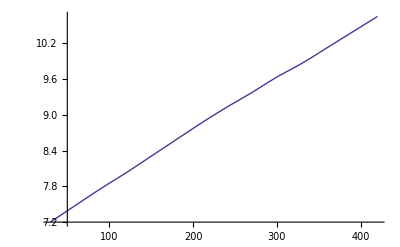

```mathematica
Plot[f2[x],{x,30,420}]
```

```mathematica
10.8731/0.012261339264978263
```

886.779

```mathematica
17.273^2/27.44
```

10.8731

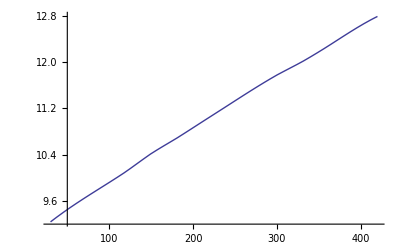

```mathematica
Plot[f3[x],{x,30,420}]
```

```mathematica
List41=ReadList["tmp",Number];
List42=Table[{i*30,List41[[i]]},{i,1,14}];
f4=Interpolation[List42];
List43={};
For[i=1,i≤12,i++,
AppendTo[List43,D[f4[x],x]/.x->(30+30*i)]]
LinearModelFit[Table[{List41[[i+1]]^(5/4),List43[[i]]},{i,1,12}],x,x]//Normal
```

0.0206952-0.000799615 x

```mathematica
13.557/0.0184913
```

733.156

```mathematica
List42
```

{{30,11.5776},{60,11.8714},{90,12.2793},{120,12.5077},{150,12.8663},{180,13.0781},{210,13.3388},{240,13.6807},{270,13.9411},{300,14.2502},{330,14.5429},{360,14.8192},{390,15.0792},{420,15.3553}}

```mathematica
List43
```

{0.0133276,0.0122355,0.00806114,0.0110476,0.00678782,0.00986214,0.0109434,0.00876823,0.0103916,0.00948366,0.00893812,0.00875409}

```mathematica
(12.2793-11.5776)/60
```

0.011695

```mathematica
List41=ReadList["tmp",Number];
List42=Table[{i*30,List41[[i]]},{i,1,14}];
f4=Interpolation[List42];
List43={};
For[i=1,i≤12,i++,
AppendTo[List43,D[f4[x],x]/.x->(30+30*i)]]
LinearModelFit[Table[{List41[[i+1]]^(5/4),List43[[i]]},{i,1,12}],x,x]//Normal
```

0.0103163-0.000184185 x

```mathematica
6.847/0.0103163
```

663.707